```mathematica
z1=18;
z2=21;
z={z1,z2};
u=z2/z1;
m=2.5;
β=0;
α=αt=20Degree;
ha=1.;
hf=1.25;
hl=2ha;
ρf=0.38;
c=0.25;
x2=0.5;
```

```mathematica
r=m z/2
rb=m z Cos[α]/2
pt=Pi m
s0=Pi m/2
ro=c m/(1-Sin[αt])
p1=m z1 Sin[180Degree/z1]
zmin=2ha/Sin[α]^2
xmin=ha  (zmin-z)/zmin
```

{22.5,26.25}

{21.1431,24.6669}

7.85398

3.92699

0.949877

7.81417

17.0973

{-0.0528,-0.228267}

```mathematica
y1[x_]:=(z1/2+z2/2)*(Cos[αt]/Cos[76.44*((Tan[αt]-αt)+2*(x2+x)*Tan[αt]/(z1+z2))^0.3189*Pi/180]-1)
αwt[x_]:=77.1*((Tan[αt]-αt)+2*(x2+x)*Tan[αt]/(z1+z2))^0.3214Pi/180
dy[x_]:=x+x2-y1[x]
rw1[x_]:=m z1 Cos[αt]/(2Cos[αwt[x]])
rw2[x_]:=m z2 Cos[αt]/(2Cos[αwt[x]])
aw[x_]:=rw1[x]+rw2[x]
ra1[x_]:=m(z1/2+ha+x-dy[x])
ra2[x_]:=m(z2/2+ha+x2-dy[x])
rf1[x_]:=m(z1/2-ha+x-c)
rf2[x_]:=m(z2/2-ha+x2-c)
h[x_]:=m(2ha+c-dy[x])
s1[x_]:=m(Pi/2+2x Tan[αt])
s2[x_]:=m(Pi/2+2x2 Tan[αt])
αa1[x_]:=ArcCos[rb[[1]]/ra1[x]]
αa2[x_]:=ArcCos[rb[[2]]/ra2[x]]
sa1[x_]:=2ra1[x](s1[x]/(2r[[1]])+Tan[αt]-αt-Tan[ArcCos[rb[[1]]/ra1[x]]]+ArcCos[rb[[1]]/ra1[x]])
sa2[x_]:=2ra2[x](s2[x]/(2r[[2]])+Tan[αt]-αt-Tan[ArcCos[rb[[2]]/ra2[x]]]+ArcCos[rb[[2]]/ra2[x]])
ϵα[x_]:=z1/(2Pi)(Tan[αa1[x]]-Tan[αwt[x]])+z2/(2Pi)(Tan[αa2[x]]-Tan[αwt[x]])
ϵγ[x_]:=ϵα[x]+2/Pi Sin[β]
λ1[x_]:=(z2(Tan[αa2[x]]-Tan[αwt[x]]))/((z1+z2)Tan[αwt[x]]-z2 Tan[αa2[x]])(1+z1/z2) 
λ2[x_]:=(z1(Tan[αa1[x]]-Tan[αwt[x]]))/((z1+z2)Tan[αwt[x]]-z1 Tan[αa1[x]])(1+z1/z2) 
θ[x_]:=2(z1+z2)/(z1*z2*Tan[αwt[x]]*Cos[αt])
```

```mathematica
xx=Table[x,{x,0,1.6,0.1}];
names={"x1","y1","dy","rw1","rw2","aw","ra1","ra2","rf1","rf2","h","s1","s2","alfwt","sa1","sa2","ealf","egam","lam1","lam2","teta"};
Grid[Prepend[{xx,y1[xx],dy[xx],rw1[xx],rw2[xx],aw[Table[x,{x,0,1.6,0.1}]],ra1[xx],ra2[xx],rf1[xx],Table[1,{i,17}]*rf2[xx],h[xx],s1[xx],Table[1,{i,17}]*s2[xx],180/Pi αwt[xx],sa1[xx],sa2[xx],ϵα[xx],ϵγ[xx],λ1[xx],λ2[xx],θ[xx]}ᵀ,names],Frame->All,Spacings->{Automatic, 1},ItemSize->All]
```

x1 | y1 | dy | rw1 | rw2 | aw | ra1 | ra2 | rf1 | rf2 | h | s1 | s2 | alfwt | sa1 | sa2 | ealf | egam | lam1 | lam2 | teta
0. | 0.457336 | 0.0426638 | 23.0249 | 26.8623 | 49.8872 | 24.8933 | 29.8933 | 19.375 | 24.375 | 5.51834 | 3.92699 | 4.83692 | 23.3252 | 1.83019 | 1.3606 | 1.39198 | 1.39198 | 4.04977 | 1.12972 | 0.50927
0.1 | 0.542645 | 0.0573553 | 23.1239 | 26.9779 | 50.1018 | 25.1066 | 29.8566 | 19.625 | 24.375 | 5.48161 | 4.10898 | 4.83692 | 23.8881 | 1.77867 | 1.40909 | 1.36469 | 1.36469 | 3.15827 | 1.14882 | 0.495817
0.2 | 0.626362 | 0.0736381 | 23.2212 | 27.0914 | 50.3125 | 25.3159 | 29.8159 | 19.875 | 24.375 | 5.4409 | 4.29096 | 4.83692 | 24.4243 | 1.72527 | 1.46253 | 1.33719 | 1.33719 | 2.54068 | 1.16657 | 0.483544
0.3 | 0.708647 | 0.0913526 | 23.3168 | 27.2029 | 50.5197 | 25.5216 | 29.7716 | 20.125 | 24.375 | 5.39662 | 4.47295 | 4.83692 | 24.9367 | 1.67004 | 1.52032 | 1.30947 | 1.30947 | 2.0862 | 1.1832 | 0.472279
0.4 | 0.789637 | 0.110363 | 23.411 | 27.3128 | 50.7238 | 25.7241 | 29.7241 | 20.375 | 24.375 | 5.34909 | 4.65493 | 4.83692 | 25.4278 | 1.61305 | 1.58191 | 1.28155 | 1.28155 | 1.73678 | 1.19885 | 0.461883
0.5 | 0.869448 | 0.130552 | 23.5038 | 27.4211 | 50.9249 | 25.9236 | 29.6736 | 20.625 | 24.375 | 5.29862 | 4.83692 | 4.83692 | 25.8996 | 1.55432 | 1.64685 | 1.25344 | 1.25344 | 1.45908 | 1.21366 | 0.45224
0.6 | 0.948181 | 0.151819 | 23.5954 | 27.5279 | 51.1233 | 26.1205 | 29.6205 | 20.875 | 24.375 | 5.24545 | 5.0189 | 4.83692 | 26.354 | 1.49388 | 1.71474 | 1.22514 | 1.22514 | 1.23257 | 1.22775 | 0.443259
0.7 | 1.02593 | 0.174074 | 23.6859 | 27.6335 | 51.3194 | 26.3148 | 29.5648 | 21.125 | 24.375 | 5.18981 | 5.20089 | 4.83692 | 26.7924 | 1.43176 | 1.7852 | 1.19666 | 1.19666 | 1.0439 | 1.2412 | 0.434863
0.8 | 1.10276 | 0.19724 | 23.7753 | 27.7379 | 51.5132 | 26.5069 | 29.5069 | 21.375 | 24.375 | 5.1319 | 5.38287 | 4.83692 | 27.2161 | 1.36798 | 1.85791 | 1.16799 | 1.16799 | 0.884022 | 1.25408 | 0.426985
0.9 | 1.17875 | 0.221247 | 23.8638 | 27.8411 | 51.7049 | 26.6969 | 29.4469 | 21.625 | 24.375 | 5.07188 | 5.56486 | 4.83692 | 27.6264 | 1.30256 | 1.93258 | 1.13915 | 1.13915 | 0.746573 | 1.26647 | 0.41957
1. | 1.25397 | 0.246034 | 23.9514 | 27.9433 | 51.8947 | 26.8849 | 29.3849 | 21.875 | 24.375 | 5.00992 | 5.74684 | 4.83692 | 28.0242 | 1.23551 | 2.00895 | 1.11012 | 1.11012 | 0.626953 | 1.2784 | 0.412573
1.1 | 1.32846 | 0.271545 | 24.0382 | 28.0446 | 52.0827 | 27.0711 | 29.3211 | 22.125 | 24.375 | 4.94614 | 5.92883 | 4.83692 | 28.4104 | 1.16683 | 2.08677 | 1.08092 | 1.08092 | 0.521748 | 1.28993 | 0.405951
1.2 | 1.40227 | 0.297729 | 24.1242 | 28.1449 | 52.2691 | 27.2557 | 29.2557 | 22.375 | 24.375 | 4.88068 | 6.11081 | 4.83692 | 28.7858 | 1.09654 | 2.16583 | 1.05153 | 1.05153 | 0.428374 | 1.3011 | 0.399671
1.3 | 1.47546 | 0.324543 | 24.2095 | 28.2445 | 52.454 | 27.4386 | 29.1886 | 22.625 | 24.375 | 4.81364 | 6.2928 | 4.83692 | 29.1512 | 1.02464 | 2.24593 | 1.02197 | 1.02197 | 0.344833 | 1.31194 | 0.393701
1.4 | 1.54805 | 0.351945 | 24.2942 | 28.3432 | 52.6374 | 27.6201 | 29.1201 | 22.875 | 24.375 | 4.74514 | 6.47478 | 4.83692 | 29.5072 | 0.951139 | 2.32688 | 0.992222 | 0.992222 | 0.269559 | 1.32248 | 0.388015
1.5 | 1.6201 | 0.379898 | 24.3782 | 28.4412 | 52.8195 | 27.8003 | 29.0503 | 23.125 | 24.375 | 4.67525 | 6.65677 | 4.83692 | 29.8543 | 0.87603 | 2.4085 | 0.962289 | 0.962289 | 0.201305 | 1.33275 | 0.382589
1.6 | 1.69163 | 0.408367 | 24.4617 | 28.5386 | 53.0003 | 27.9791 | 28.9791 | 23.375 | 24.375 | 4.60408 | 6.83875 | 4.83692 | 30.1931 | 0.799318 | 2.49066 | 0.932169 | 0.932169 | 0.139067 | 1.34277 | 0.377403

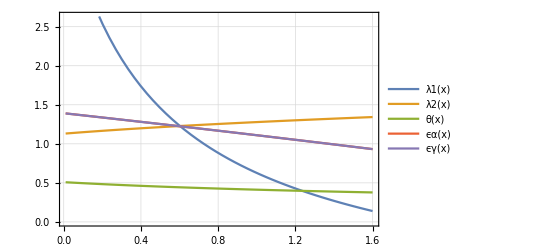

```mathematica
Plot[{λ1[x],λ2[x],θ[x],ϵα[x],ϵγ[x]},{x,0.01,1.6},PlotTheme->"Detailed"]
```

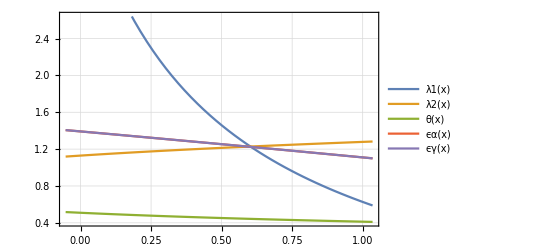

```mathematica
Plot[{λ1[x],λ2[x],θ[x],ϵα[x],ϵγ[x]},{x,xmin[[1]],xmax},PlotTheme->"Detailed"]
```

```mathematica
Clear[ϵα]
```

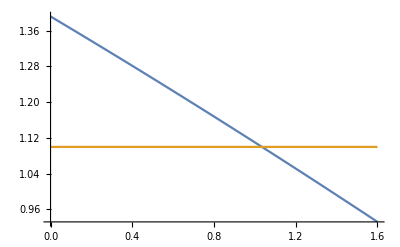

```mathematica
Plot[{ϵα[x],1.1},{x,0,1.6}]
```

```mathematica
xmax=1.035
```

1.035

```mathematica
ϵα[xmax]
```

1.09992

```mathematica
NSolve[ϵα[x]==1.1,x]
```

$Aborted

```mathematica
ϵα[xmin[[1]]]-1.1
```

0.306295

```mathematica
xmin
```

{-0.0528,-0.228267}